# ToW Zone Extent

We want to find how far the ToW zone extends for the various experimental geometries. The setup is like this:

-Graphics-

Above is a top down view, below is a view looking through side a

-Graphics-

## Derivation of ToW zone extent

To find d, the extent of the ToW zone, we can use some trig. Pythagorean theorem on the red triangle gives

```mathematica
eq1=a==Sqrt[(2R+2L)^2-s^2]
```

a==√((2 L+2 R)^2-s^2)

Then the sine of θ in the blue triangle is

```mathematica
eq2=Sin[θ]==a/d
```

Sin[θ]==a/d

Solve this to find

```mathematica
soln=Solve[{eq1,eq2},d,{a}]//Simplify
```

{{d→√((2 L+2 R-s) (2 L+2 R+s)) Csc[θ]}}

So our solution is

```mathematica
ToWzone=d/.soln[[1]]//FullSimplify
```

√(4 (L+R)^2-s^2) Csc[θ]

```mathematica
CForm[ToWzone]
```

Sqrt((2*L + 2*R - s)*(2*L + 2*R + s))*Csc(θ)

## Testing

We should make sure this function behaves as it should. First, as θ gets close to 0 or π, the ToW zone should become infinitely long

```mathematica
Simplify[Limit[ToWzone,θ->0],Assumptions->{0<L<Infinity,0<R<Infinity,0<s<2L+2R}]
```

∞

```mathematica
Simplify[Limit[ToWzone,θ->Pi],Assumptions->{0<L<Infinity,0<R<Infinity,0<s<2L+2R}]
```

-∞

The situation is somewhat more simple for case where s→0, where the geometry looks like this

-Graphics-

From this we can see that in this geometry

```mathematica
Solve[Sin[θ]==(2L+2R)/d,d]
```

{{d→2 (L+R) Csc[θ]}}

The full solution should match this

```mathematica
Simplify[Limit[ToWzone,s->0],Assumptions->{L>0,R>0,s>0,0<θ<Pi}]
```

2 (L+R) Csc[θ]

```mathematica
Simplify[Limit[ToWzone,s->0]/.θ->Pi/2,Assumptions->{L>0,R>0,s>0}]
```

2 (L+R)

-Graphics-

```mathematica
Sqrt[(2R+2L)^2-s^2]//Simplify
```

√(4 (L+R)^2-s^2)

```mathematica
ToWzone/.θ->Pi/2//FullSimplify
```

√(4 (L+R)^2-s^2)

## Investigation of ToW zone

We can plot the extent of the ToW zone as a function of θ

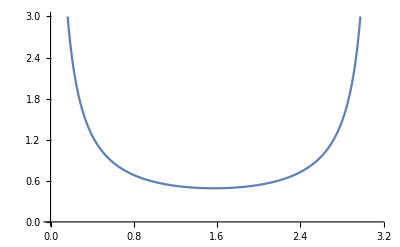

```mathematica
Plot[ToWzone/.{L->.057,R->.5,s->1},{θ,0,Pi},PlotRange->{0,3}]
```

As well as find the values for each of the experimental geometries

```mathematica
TableForm[ToWzone/.{L->.057,R->.5}/.
{{{s->0,θ->30°},{s->0,θ->90°},{s->0,θ->150°}},{{s->.5,θ->30°},{s->.5,θ->90°},{s->.5,θ->150°}},
{{s->1,θ->30°},{s->1,θ->90°},{s->1,θ->150°}}}
,TableHeadings->{{0,.5,1},{"Acute","Normal","Obtuse"}}]
```

| Acute | Normal | Obtuse
0 | 2.228 | 1.114 | 2.228
0.5 | 1.99098 | 0.995488 | 1.99098
1 | 0.981827 | 0.490913 | 0.981827

## Estimation of ToW Fraction from ToW zone

We can make a simple estimate of the ToW fraction just by assuming there is a rate war between leaving the ToW zone and binding

```mathematica
p=konMacro/(konMacro+v/(2*ToWzone))
```

konMacro/(konMacro+(v Sin[θ])/(2 √(4 (L+R)^2-s^2)))

```mathematica
?Sin
```

Sin[z] gives the sine of z.

```mathematica
pdeg=p/.Sin[θ]->Sin[θ Degree]
```

konMacro/(konMacro+(v Sin[° θ])/(2 √(4 (L+R)^2-s^2)))

```mathematica
konMacroRule=konMacro->konMicro*n*(1/2*4/3*Pi*L^3)/(4/3Pi ((R+L)^3-R^3))
```

konMacro→(konMicro L^3 n)/(2 (-R^3+(L+R)^3))

```mathematica
pofs[ss_]:=p/.konMacroRule/.{konMicro->25,n->15,L->.057,R->.5,s->ss,v->1}
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
CI[f_,n_]:=1.96*Sqrt[f(1-f)/n];
```

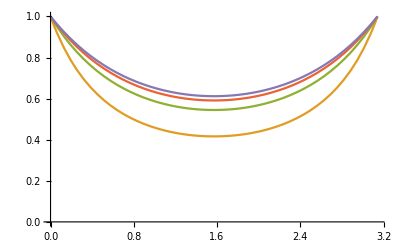

```mathematica
Plot[pofs[s]/.s->{1.25,1,.75,.5,.25},{θ,0,Pi},PlotRange->{0,1},Evaluated->True]
```

```mathematica
data1000=Partition[Riffle[{{30*Pi/180,.58},{90*Pi/180,.46},{150*Pi/180,.64}},ErrorBar/@CI[{.58,.46,.64},{36,95,44}]],2]
data500=Partition[Riffle[{{30*Pi/180,.83},{90*Pi/180,.7},{150*Pi/180,.8}},ErrorBar/@CI[{.83,.7,.8},{46,60,40}]],2]
```

{{{π/6,0.58},ErrorBar[0.161229]},{{π/2,0.46},ErrorBar[0.100224]},{{(5 π)/6,0.64},ErrorBar[0.141831]}}

{{{π/6,0.83},ErrorBar[0.108553]},{{π/2,0.7},ErrorBar[0.115955]},{{(5 π)/6,0.8},ErrorBar[0.123961]}}

```mathematica
data1000deg=Partition[Riffle[{{30,.58},{90,.46},{150,.64}},ErrorBar/@CI[{.58,.46,.64},{36,95,44}]],2]
data500deg=Partition[Riffle[{{30,.83},{90,.7},{150,.8}},ErrorBar/@CI[{.83,.7,.8},{46,60,40}]],2]
data0deg=Partition[Riffle[{{30,.79},{90,.93},{150,.89}},ErrorBar/@CI[{.79,.93,.89},{38,59,27}]],2]
```

{{{30,0.58},ErrorBar[0.161229]},{{90,0.46},ErrorBar[0.100224]},{{150,0.64},ErrorBar[0.141831]}}

{{{30,0.83},ErrorBar[0.108553]},{{90,0.7},ErrorBar[0.115955]},{{150,0.8},ErrorBar[0.123961]}}

{{{30,0.79},ErrorBar[0.129505]},{{90,0.93},ErrorBar[0.0651059]},{{150,0.89},ErrorBar[0.118023]}}

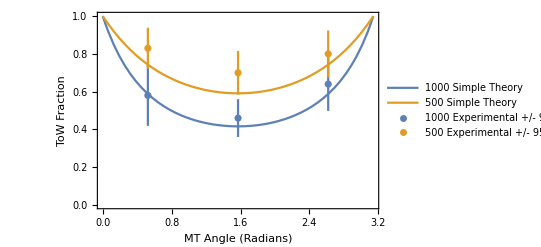

```mathematica
Show[
Plot[Evaluate[pofs[s]/.{konMacroRule}/.s->{1,.5}],{θ,0,Pi},PlotRange->{0,1},Evaluated->True,PlotLegends->{"1000 Simple Theory","500 Simple Theory"}],
ErrorListPlot[{data1000,data500},PlotLegends->{"1000 Experimental +/- 95% CI","500 Experimental +/- 95% CI"}],Frame->True,FrameLabel->{"MT Angle (Radians)","ToW Fraction"}
]
```

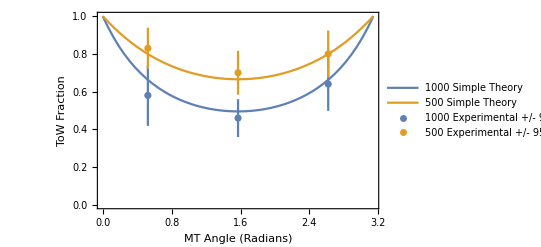

```mathematica
Show[
Plot[Evaluate[p/.{konMacro->2,n->15,L->.057,R->.5,v->1}/.s->{1,.5}],{θ,0,Pi},PlotRange->{0,1},Evaluated->True,PlotLegends->{"1000 Simple Theory","500 Simple Theory"}],
ErrorListPlot[{data500,data1000},PlotLegends->{"1000 Experimental +/- 95% CI","500 Experimental +/- 95% CI"}],Frame->True,FrameLabel->{"MT Angle (Radians)","ToW Fraction"}
]
```

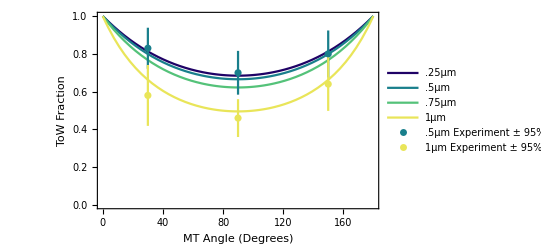

```mathematica
Show[
Plot[Evaluate[pdeg/.{konMacro->1,n->15,L->.057,R->.5,v->1}/.s->{.25,.5,.75,1}],{θ,0,180},PlotRange->{0,1},Evaluated->True,PlotLegends->Placed[{".25μm",".5μm",".75μm","1μm"},{Right,Bottom}],PlotStyle->ColorData["BlueGreenYellow"]/@Range[0,1,1/3]],
ErrorListPlot[{data500deg,data1000deg},PlotLegends->Placed[{".5μm Experiment ± 95% CI","1μm Experiment ± 95% CI"},{Left,Bottom}],PlotStyle->{ColorData["BlueGreenYellow"][1/3],ColorData["BlueGreenYellow"][1]}],Frame->True,FrameLabel->{"MT Angle (Degrees)","ToW Fraction"}
]
```

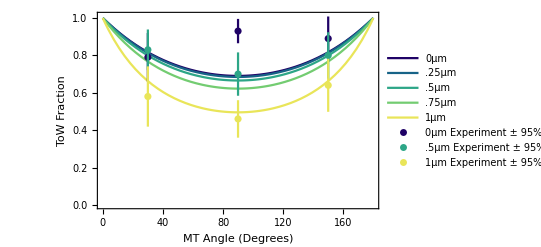

```mathematica
Show[
Plot[Evaluate[pdeg/.{konMacro->1,n->15,L->.057,R->.5,v->1}/.s->{0,.25,.5,.75,1}],{θ,0,180},PlotRange->{0,1.01},Evaluated->True,PlotLegends->Placed[{"0μm",".25μm",".5μm",".75μm","1μm"},{Right,Bottom}],PlotStyle->ColorData["BlueGreenYellow"]/@Range[0,1,1/4]],
ErrorListPlot[{data0deg,data500deg,data1000deg},PlotLegends->Placed[{"0μm Experiment ± 95% CI",".5μm Experiment ± 95% CI","1μm Experiment ± 95% CI"},{Left,Bottom}],PlotStyle->{ColorData["BlueGreenYellow"][0],ColorData["BlueGreenYellow"][1/2],ColorData["BlueGreenYellow"][1]}],Frame->True,FrameLabel->{"MT Angle (Degrees)","ToW Fraction"}
]
```

```mathematica
Export["blah.pdf",%]
```

blah.pdf

```mathematica
Manipulate[Show[
Plot[Evaluate[p/.{konMacro->k,L->.057,R->.5,v->1}/.s->{1,.5}],{θ,0,Pi},PlotRange->{0,1},Evaluated->True,PlotLegends->{"1000 Simple Theory","500 Simple Theory"}],
ErrorListPlot[{data1000,data500},PlotLegends->{"1000 Experimental +/- 95% CI","500 Experimental +/- 95% CI"}],Frame->True,FrameLabel->{"MT Angle (Radians)","ToW Fraction"}
],{k,.001,10}]
```